# Inlämningsuppgift 1: Problemlösning

## Lösningar

### Polynomekvation

För att hitta lösningarna till polynomekvationen: 2 x^4+28/3 x^3-22/3 x^2-140/3 x+16=0. 
Använder jag funktionen Solve[] där den ska lösa variabeln x.

```mathematica
{x1,x2,x3,x4}=x/.Solve[2 x^4+28/3 x^3-22/3 x^2-140/3 x+16==0]
```

{-4,-3,1/3,2}

Jag använder x1, x2 ... för att spara ekvationens nollställen/skärningspunkter på de värderna för att sedan använda dem när jag ska rita grafen.

För att plotta grafen används funktionen Plot, där jag använder Axeslabel för att ge horisontal planet namnet x och vertikal planet till y. Epilog används för att få punkter på nollställena där efter väljer jag färgen röd samt punkternas storlek och vart punkterna ska vara någonstans (Point)

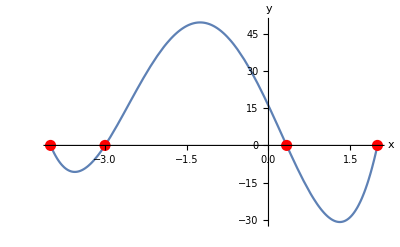

```mathematica
Plot[2 x^4+(28 x^3)/3-(22 x^2)/3-(140 x)/3+16,{x,2,-4},AxesLabel->{"x","y"},Epilog ->{Red,PointSize[0.02],
Point[{x1,0}],
Point[{x2,0}],
Point[{x3,0}],
Point[{x4,0}]
}
]
```

### Olikhet

### Binomisk ekvation

```mathematica
För att hitta lössningarna till den komplexa ekvationen: z=-3+3i
```

att den För hitta komplexa lössningarna till (ekvationen:-3+3 i)

```mathematica
{z1,z2,z3,z4,z5}=z/.Solve[z^5 == -3 + 3*I]
```

{-3+3 Root0.560+0.0696 ⅈRoot[{1+#1^2&,-240-3 #1+1215 #2-2430 #2^2+2430 #2^3-1215 #2^4+243 #2^5&},{2,1}]0.560432147724209,-3+3 Root0.798-0.397 ⅈRoot[{1+#1^2&,-240-3 #1+1215 #2-2430 #2^2+2430 #2^3-1215 #2^4+243 #2^5&},{2,2}]0.797952835199128,-3+3 Root0.930+0.440 ⅈRoot[{1+#1^2&,-240-3 #1+1215 #2-2430 #2^2+2430 #2^3-1215 #2^4+243 #2^5&},{2,3}]0.9303792917326404,-3+3 Root1.31-0.315 ⅈRoot[{1+#1^2&,-240-3 #1+1215 #2-2430 #2^2+2430 #2^3-1215 #2^4+243 #2^5&},{2,4}]1.3146958370983006,-3+3 Root1.40+0.202 ⅈRoot[{1+#1^2&,-240-3 #1+1215 #2-2430 #2^2+2430 #2^3-1215 #2^4+243 #2^5&},{2,5}]1.3965398882457218}

```mathematica
cn={N[z1],N[z2],N[z3],N[z4],N[z5]}
```

{-1.3187+0.208862 ⅈ,-0.606141-1.18962 ⅈ,-0.208862+1.3187 ⅈ,0.944088-0.944088 ⅈ,1.18962+0.606141 ⅈ}

```mathematica
pp=Table[{Re[cn[[i]]], Im[cn[[i]]]}, {i, 1, 5}]
```

```mathematica
{{-1.3187035568273728,0.20886212480207877},{-0.6061414944026162,-1.1896196647371657},{-0.20886212480207877,1.3187035568273728},{0.9440875112949021,-0.9440875112949021},{1.1896196647371653,0.6061414944026161}}
z1 = -1.3187035568273728+0.20886212480207877I
```

{{-1.3187,0.208862},{-0.606141,-1.18962},{-0.208862,1.3187},{0.944088,-0.944088},{1.18962,0.606141}}

-1.3187+0.208862 ⅈ

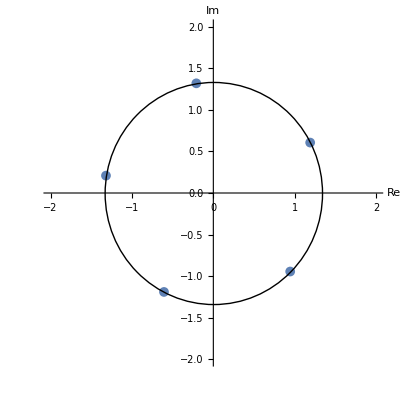

```mathematica
ListPlot[pp, PlotRange ->{{-2,2},{-2,2}}, AxesLabel->{"Re", "Im"}, AspectRatio->Automatic,PlotMarkers->{Automatic, Medium},Epilog->{ EdgeForm[Red],FaceForm[],Circle[{0,0 },Abs[z1]]}]
```

### Arean av en cirkel och närmevärde till Pi

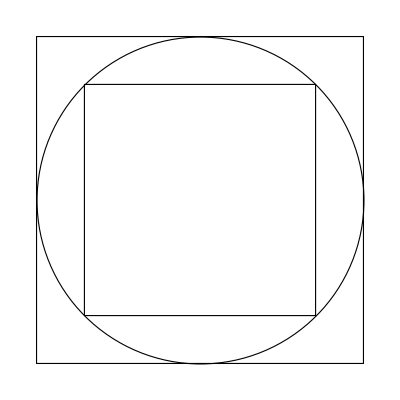

```mathematica
Show[Graphics[{FaceForm[None],EdgeForm[{Black}],Polygon[{{-1/Sqrt[2],-1/Sqrt[2]},{-1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],1/Sqrt[2]} ,{1/Sqrt[2], -1/Sqrt[2]}}],Disk[{0, 0}],Polygon[{{-1, -1}, {-1, 1},{1, 1},{1, -1}}]}]]
```

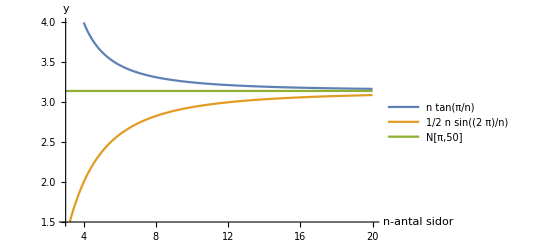

```mathematica
Plot[{n*Tan[Pi/n],(n*Sin[2Pi/n])/2, N[Pi,50]}, {n,3, 20},PlotRange->{1.5,4}, AxesLabel->{"n-antal sidor","y"}, PlotLegends->"Expressions"]
```